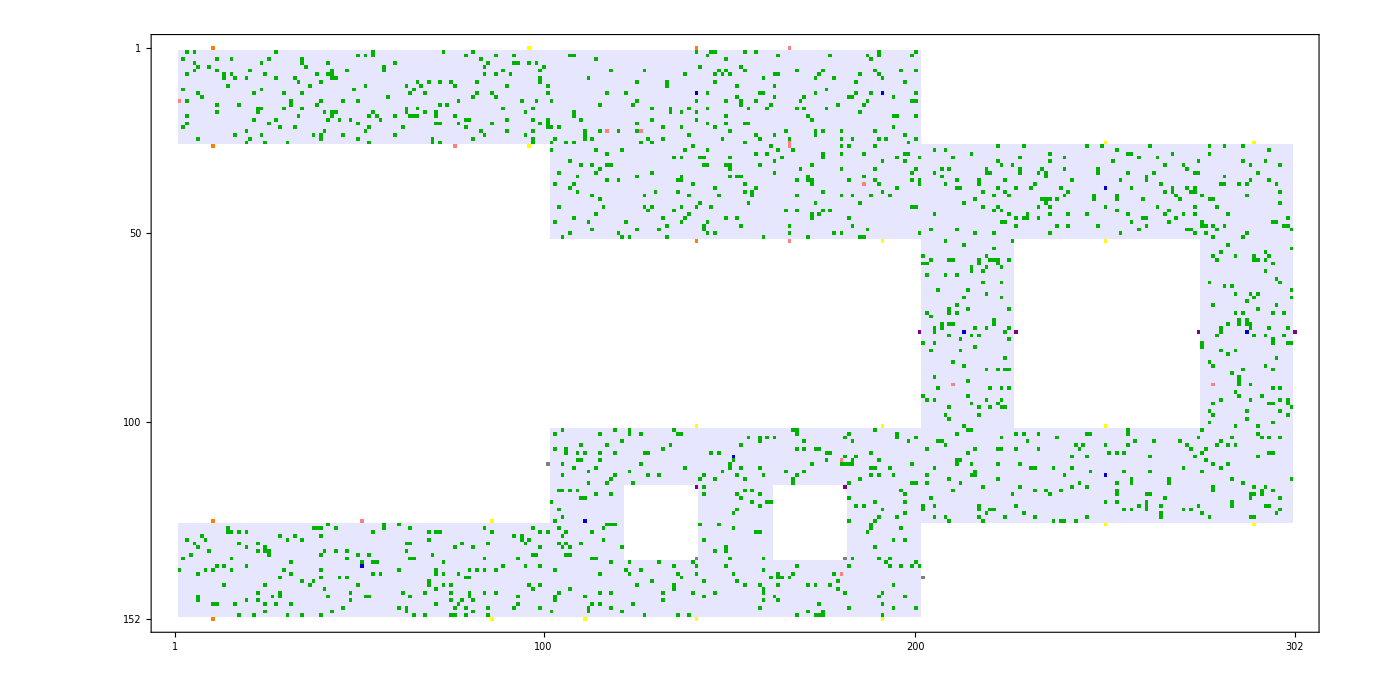

```mathematica
(*mRegion={{{2,26},{2,101}},{{2,51},{102,201}},{{27,101},{202,226}},{{27,51},{227,301}},{{52,126},{277,301}},{{102,126},{202,276}},{{102,136},{182,201}},{{102,116},{102,181}},{{117,136},{142,161}},{{117,136},{102,121}},{{137,151},{102,201}},{{127,151},{2,101}}};
RegionNum={50,100,80,80,80,80,60,100,60,150,100,60};
nPPL=Sum[RegionNum[[i]],{i,1,Length[RegionNum]}];*)
nPPL=1500;
currentPPL=nPPL;
nPPLUB=10000;
nESC=0;
nTime=500;
VLen=12;
VLenIns=18;
PPLThreshold=5;
PPLFlow=5;
Aim=Table[0,{i,1,nPPLUB}];
CollisionThreshold=2;
MAX=10000000;
PPLPath=Table[{-1,-1},{i,1,nPPLUB},{j,1,nTime}];
Location=Table[{-1,-1},{i,1,nPPLUB}];
(*Instructors={};*)
Instructors={{15,2},{23,117},{23,126},{37,186},{90,210},{90,280},{110,180},{140,180}};(*Instructor's Position*)
nInstUB=50;
InstPath=Table[{-1,-1},{i,1,nInstUB},{j,1,nTime}];
Escape=Table[0,{i,1,nTime}];
For[
mi=1,
mi≤Min[Length[Instructors],nInstUB],
mi++,
InstPath[[mi]][[1]]=Instructors[[mi]];
]
Model=Table[Table[0,{mi,1,152},{mj,1,302}],{mk,1,nTime}];
(*initialize the structure of the floor*)
(*Source={};
PPLReservoir={};
LeftP={};
RightP={};
UpP={};
DownP={};*)
Source={{138,51},{13,141},{13,191},{126,111},{109,151},{76,213},{76,289},{38,251},{114,251}};
PPLReservoir={300,300,300,300,300,300,300,300,300};
Exits={{27,76},{126,51},{1,166},{52,166},{26,166},{27,166}};
Dirc={{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}};
LeftP={{1,96},{27,96},{101,141},{126,86},{152,86},{152,141},{26,251},{52,251},{127,251},{101,251},{26,291},{127,291},{152,111},{152,191},{52,191},{101,191}};
RightP={{1,11},{27,11},{1,141},{52,141},{126,11},{152,11}};
UpP={{76,201},{76,302},{76,227},{76,276},{117,141},{117,181}};
DownP={{141,202},{111,101},{136,141},{136,181}};
NullP={};
Poster=Union[LeftP,RightP,UpP,DownP];
distExt=Table[MAX,{i,1,Length[Exits]}];
distG=Table[MAX,{i,1,nInstUB}];
distP=Table[MAX,{i,1,Length[Poster]}];
PIndex=Table[0,{i,1,152},{j,1,302}];
CollisionReport=Table[Table[0,{mi,1,152},{mj,1,302}],{mk,1,nTime}];
defaultMode=Table[0,{i,1,nPPLUB}];
CollisionCnt=Table[0,{i,1,nPPLUB}];
TimeCnt=Table[-1,{i,1,nPPLUB}];
CollisionPunishment=Table[0,{i,1,nPPLUB}];
PunishmentPeriod=15;

For[
mi=27,
mi≤126,
mi++,
{
For[
mj=2,
mj≤101,
mj++,
{
Model[[1]][[mi]][[mj]]=1;
}
]
}
]
For[
mi=52,
mi<=101,
mi++,
{
For[
mj=102,
mj≤201,
mj++,
{
Model[[1]][[mi]][[mj]]=1;
}
]
}
]
For[
mj=202,
mj≤301,
mj++,
{
For[
mi=2,
mi≤26,
mi++,
{
Model[[1]][[mi]][[mj]]=1;
Model[[1]][[mi+125]][[mj]]=1;
}
]
}
]
For[
mi=52,
mi≤101,
mi++,
{
For[
mj=227,
mj≤276,
mj++,
{
Model[[1]][[mi]][[mj]]=1;
}
]
}
]
For[
mi=117,
mi≤136,
mi++,
{
For[
mj=122,
mj≤141,
mj++,
{
Model[[1]][[mi]][[mj]]=1;
Model[[1]][[mi]][[mj+40]]=1;
}
]
}
]
For[
mi=1,
mi≤152,
mi++,
{
Model[[1]][[mi]][[1]]=1;
Model[[1]][[mi]][[302]]=1;
}
]
For[
mj=1,
mj≤302,
mj++,
{
Model[[1]][[1]][[mj]]=1;
Model[[1]][[152]][[mj]]=1;
}
]
(*Draw elevators and exits*)
Model[[1]][[27]][[76]]=3;
Model[[1]][[126]][[51]]=3;
Model[[1]][[1]][[166]]=3;
Model[[1]][[26]][[166]]=3;
Model[[1]][[27]][[166]]=3;
Model[[1]][[52]][[166]]=3;
Model[[1]][[138]][[51]]=2;
Model[[1]][[13]][[141]]=2;
Model[[1]][[13]][[191]]=2;
Model[[1]][[126]][[111]]=2;
Model[[1]][[109]][[151]]=2;
Model[[1]][[76]][[213]]=2;
Model[[1]][[76]][[289]]=2;
Model[[1]][[38]][[251]]=2;
Model[[1]][[114]][[251]]=2;
For[
mm=1,
mm≤Length[LeftP],
mm++,
{
Model[[1]][[LeftP[[mm]][[1]]]][[LeftP[[mm]][[2]]]]=5;
}
];
For[
mm=1,
mm≤Length[RightP],
mm++,
{
Model[[1]][[RightP[[mm]][[1]]]][[RightP[[mm]][[2]]]]=6;
}
];
For[
mm=1,
mm≤Length[UpP],
mm++,
{
Model[[1]][[UpP[[mm]][[1]]]][[UpP[[mm]][[2]]]]=7;
}
];
For[
mm=1,
mm≤Length[DownP],
mm++,
{
Model[[1]][[DownP[[mm]][[1]]]][[DownP[[mm]][[2]]]]=8;
}
];
For[
mm=1,
mm≤Length[NullP],
mm++,
{
Model[[1]][[NullP[[mm]][[1]]]][[NullP[[mm]][[2]]]]=9;
}
];
For[
mi=1,
mi≤Min[Length[Instructors],nInstUB],
mi++,
{
Model[[1]][[InstPath[[mi]][[1]][[1]]]][[InstPath[[mi]][[1]][[2]]]]=10;
}
]
(*Randomly distributed people*)
(*cntPPL=0;
For[
mi=1,
mi≤Length[mRegion],
mi++,
{
For[
mj=1,
mj≤RegionNum[[mi]],
mj++,
{
PPLx=RandomInteger[{mRegion[[mi]][[1]][[1]],mRegion[[mi]][[1]][[2]]}];
PPLy=RandomInteger[{mRegion[[mi]][[2]][[1]],mRegion[[mi]][[2]][[2]]}];
If[
Model[[1]][[PPLx]][[PPLy]]≠0,
mj=mj-1,
{
Model[[1]][[PPLx]][[PPLy]]=4;
cntPPL++;
Location[[cntPPL]]={PPLx,PPLy};
PPLPath[[cntPPL]][[1]]={PPLx,PPLy};
PIndex[[PPLx]][[PPLy]]=cntPPL;
}
];
}
];
}
]*)
For[
mi=1,
mi≤nPPL,
mi++,
{
PPLx=RandomInteger[{2,151}];
PPLy=RandomInteger[{2,301}];
If[
Model[[1]][[PPLx]][[PPLy]]≠0,
mi=mi-1,
{
Model[[1]][[PPLx]][[PPLy]]=4;
Location[[mi]]={PPLx,PPLy};
PPLPath[[mi]][[1]]={PPLx,PPLy};
PIndex[[PPLx]][[PPLy]]=mi;
}
]
}
]
MatrixPlot[Model[[1]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}](*0.Vacant,1.Impasse,2.Source,3.Exit,4.People,5.Left,6.Right,7.Up,8.Down,9.Null,10.Guide*)
```

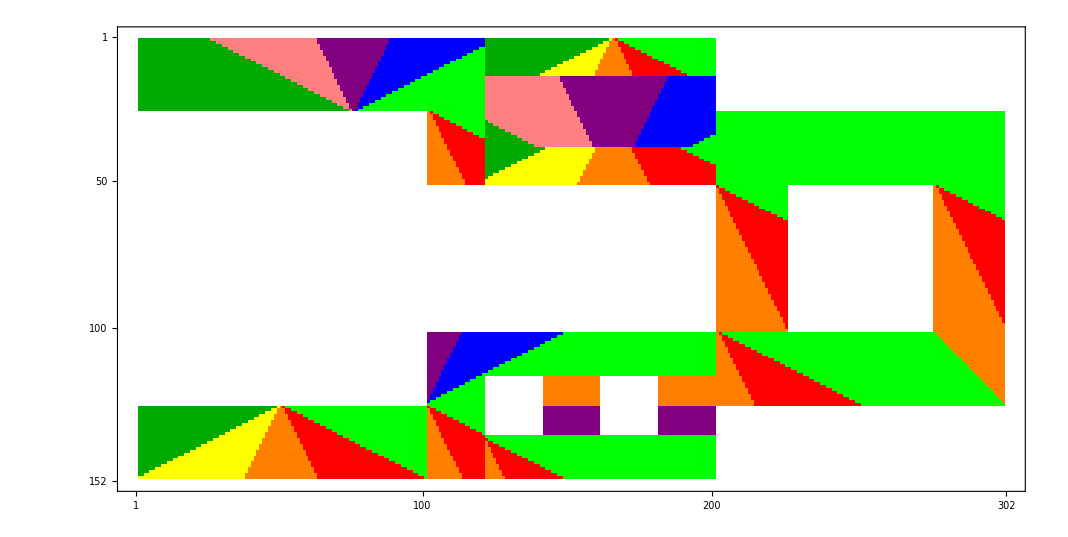

```mathematica
InsVec=Table[0,{mi,1,152},{mj,1,302}];(*Instructive Direction*)
AnchorPoints={{26,102},{51,277},{51,201},{101,202},{126,101},{137,121}};
(*Initialize the Instruction Vectors*)
For[
mi=2,
mi≤26,
mi++,
{
For[
mj=2,
mj≤121,
mj++,
{
deltai=Exits[[1]][[1]]-mi;
deltaj=Exits[[1]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=27,
mi≤51,
mi++,
{
For[
mj=102,
mj≤121,
mj++,
{
deltai=AnchorPoints[[1]][[1]]-mi;
deltaj=AnchorPoints[[1]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=2,
mi≤14,
mi++,
{
For[
mj=122,
mj≤201,
mj++,
{
deltai=Exits[[3]][[1]]-mi;
deltaj=Exits[[3]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=15,
mi≤38,
mi++,
{
For[
mj=122,
mj≤201,
mj++,
{
deltai=Exits[[4]][[1]]-mi;
deltaj=Exits[[4]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=39,
mi≤51,
mi++,
{
For[
mj=122,
mj≤201,
mj++,
{
deltai=Exits[[6]][[1]]-mi;
deltaj=Exits[[6]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=27,
mi≤51,
mi++,
{
For[
mj=202,
mj<=301,
mj++,
{
InsVec[[mi]][[mj]]=-1
}
]
}
]
For[
mi=127,
mi≤151,
mi++,
{
For[
mj=2,
mj≤101,
mj++,
{
deltai=Exits[[2]][[1]]-mi;
deltaj=Exits[[2]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=52,
mi≤101,
mi++,
{
For[
mj=277,
mj≤301,
mj++,
{
deltai=AnchorPoints[[2]][[1]]-mi;
deltaj=AnchorPoints[[2]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=102,
mi≤126,
mi++,
{
For[
mj=mi+175,
mj≤301,
mj++,
{
InsVec[[mi]][[mj]]=-3;
}
]
}
]
For[
mi=52,
mi≤101,
mi++,
{
For[
mj=202,
mj≤226,
mj++,
{
deltai=AnchorPoints[[3]][[1]]-mi;
deltaj=AnchorPoints[[3]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=102,
mi≤126,
mi++,
{
For[
mj=202,
mj≤276,
mj++,
{
deltai=AnchorPoints[[4]][[1]]-mi;
deltaj=AnchorPoints[[4]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=102,
mi≤126,
mi++,
{
For[
mj=277,
mj<mi+176,
mj++,
{
InsVec[[mi]][[mj]]=-1;
}
]
}
]
For[
mi=117,
mi≤151,
mi++,
{
For[
mj=102,
mj≤121,
mj++,
{
deltai=AnchorPoints[[5]][[1]]-mi;
deltaj=AnchorPoints[[5]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=102,
mi≤116,
mi++,
{
For[
mj=102,
mj≤201,
mj++,
{
deltai=AnchorPoints[[5]][[1]]-mi;
deltaj=AnchorPoints[[5]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=137,
mi≤151,
mi++,
{
For[
mj=122,
mj≤201,
mj++,
{
deltai=AnchorPoints[[6]][[1]]-mi;
deltaj=AnchorPoints[[6]][[2]]-mj;
si=Sign[deltai];
sj=Sign[deltaj];
If[
Abs[deltaj]≥2*Abs[deltai],
InsVec[[mi]][[mj]]=sj
];
If[
Abs[deltaj]≤1/2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si
];
If[
Abs[deltaj]>1/2*Abs[deltai] && Abs[deltaj]<2*Abs[deltai],
InsVec[[mi]][[mj]]=3*si+sj
]
}
]
}
]
For[
mi=117,
mi≤126,
mi++,
{
For[
mj=142,
mj<=161,
mj++,
{
InsVec[[mi]][[mj]]=-3;
InsVec[[mi]][[mj+40]]=-3;
InsVec[[mi+10]][[mj]]=3;
InsVec[[mi+10]][[mj+40]]=3;
}
]
}
]
MatrixPlot[InsVec,ColorRules->{-4->Red,-3->Orange,-2->Yellow,-1->Green,0->White,1->Darker[Green],2->Blue,3->Purple,4->Pink}]
```

```mathematica
(*Simulation*)
For[
tt=2,
tt≤nTime,
tt++,
{
Print[tt];
For[
mi=1,
mi≤152,
mi++,
{
For[
mj=1,
mj≤302,
mj++,
{
Model[[tt]][[mi]][[mj]]=Model[[tt-1]][[mi]][[mj]];
}
]
}
];(*Get a copy of Geos last time*)
For[(*Update the instructors first*)
mi=1,
mi≤Min[Length[Instructors],nInstUB],
mi++,
{
If[
InstPath[[mi]][[tt-1]][[1]]==-1 && InstPath[[mi]][[tt-1]][[2]]==-1,
InstPath[[mi]][[tt]]={-1,-1},
{
origX=InstPath[[mi]][[tt-1]][[1]];(*Original Position*)
origY=InstPath[[mi]][[tt-1]][[2]];
InstPath[[mi]][[tt]]=InstPath[[mi]][[tt-1]]+Dirc[[InsVec[[InstPath[[mi]][[tt-1]][[1]]]][[InstPath[[mi]][[tt-1]][[2]]]]+5]];
If[(*get rid of the Source*)
Model[[1]][[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]==2,
InstPath[[mi]][[tt]]=InstPath[[mi]][[tt]]+Dirc[[InsVec[[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]+5]]
];
If[(*exit*)
Model[[1]][[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]==3,
(*InstPath[[mi]][[tt]]={-1,-1}*)
{
}
];
If[(*Swap with ordinary people*)
InstPath[[mi]][[tt]][[1]]≠-1 && InstPath[[mi]][[tt]][[2]]≠-1 ,
{
If[
 Model[[tt]][[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]==4,
{
CollisionReport[[tt]][[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]=1;
Model[[tt]][[origX]][[origY]]=4;
Model[[tt]][[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]=10;
Location[[PIndex[[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]]]={origX,origY};
PPLPath[[PIndex[[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]]][[tt]]={origX,origY};
PIndex[[origX]][[origY]]=PIndex[[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]];
PIndex[[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]=0;
},
{
Model[[tt]][[origX]][[origY]]=0;
Model[[tt]][[InstPath[[mi]][[tt]][[1]]]][[InstPath[[mi]][[tt]][[2]]]]=10;
}
];
}
];
}
];
}
];
For[(*People rush in*)
mi=1,
mi≤Length[Source],
mi++,
{
spare=0;
SpareSpace={};
For[
mj=1,
mj≤9,
mj++,
{
If[
mj≠5 && Model[[tt]][[(Source[[mi]]+Dirc[[mj]])[[1]]]][[(Source[[mi]]+Dirc[[mj]])[[2]]]]==0,
{
spare++;
SpareSpace=Union[SpareSpace,{Source[[mi]]+Dirc[[mj]]}];
}
];
}
];
nFlow=Min[PPLReservoir[[mi]],PPLFlow,spare];
If[
nFlow<PPLFlow,
CollisionReport[[tt]][[Source[[mi]][[1]]]][[Source[[mi]][[2]]]]=1;
];
For[
mk=1,
mk≤nFlow,
mk++,
{
pos=RandomChoice[SpareSpace];
SpareSpace=Complement[SpareSpace,{pos}];
Model[[tt]][[pos[[1]]]][[pos[[2]]]]=4;
++currentPPL;
Location[[currentPPL]]={pos[[1]],pos[[2]]};
PPLPath[[currentPPL]][[tt]]={pos[[1]],pos[[2]]};
PIndex[[pos[[1]]]][[pos[[2]]]]=currentPPL;
}
];
PPLReservoir[[mi]]-=nFlow;
}
];
(*People Decision*)
For[
mp=1,
mp≤currentPPL,
mp++,
{
(*Exit Last Time*)
If[
Location[[mp]][[1]]<0 || Location[[mp]][[2]]<0,
Continue
];

For[
zi=1,
zi≤Length[Exits],
zi++,
{
If[
Abs[Exits[[zi]][[1]]-Location[[mp]][[1]]]>VLen  || Abs[Exits[[zi]][[2]]-Location[[mp]][[2]]]>VLen,
distExt[[zi]]=MAX,
distExt[[zi]]=Abs[Exits[[zi]][[1]]-Location[[mp]][[1]]]+Abs[Exits[[zi]][[2]]-Location[[mp]][[2]]]
];
}
];(*Get the distances to Exits*)
For[
zj=1,
zj≤Min[Length[Instructors],nInstUB],
zj++,
{
If[
Abs[InstPath[[zj]][[tt]][[1]]-Location[[mp]][[1]]]>VLenIns || Abs[InstPath[[zj]][[tt]][[2]]-Location[[mp]][[2]]]>VLenIns,
distG[[zj]]=MAX,
distG[[zj]]=Abs[InstPath[[zj]][[tt]][[1]]-Location[[mp]][[1]]]+Abs[InstPath[[zj]][[tt]][[2]]-Location[[mp]][[2]]]
];
}
];(*Get the distance to guide*)
For[
zm=1,
zm≤Length[Poster],
zm++,
{
If[
Abs[Poster[[zm]][[1]]-Location[[mp]][[1]]]>VLen || Abs[Poster[[zm]][[2]]-Location[[mp]][[2]]]>VLen,
distP[[zm]]=MAX,
distP[[zm]]=Abs[Poster[[zm]][[1]]-Location[[mp]][[1]]]+Abs[Poster[[zm]][[2]]-Location[[mp]][[2]]]
];
}
];(*Get the distance to Posters*)
If[
Min[distExt]<MAX && CollisionPunishment[[mp]]==0,
{
Aim[[mp]]=Ordering[distExt,1][[1]];
},(*Set aim to exit*)
{
If[
Min[distG]<MAX && CollisionPunishment[[mp]]==0,
{
Aim[[mp]]=Length[Exits]+Ordering[distG,1][[1]];(*Set aim to guide*)
},
{
NumNH=Table[0,{i,1,Length[Exits]+Min[nInstUB,Length[Instructors]]}];
For[
zk=1,
zk≤currentPPL,
zk++,
{
If[
zk≠mp && Abs[Location[[zk]][[1]]-Location[[mp]][[1]]]≤VLen && Abs[Location[[zk]][[2]]-Location[[mp]][[2]]]<VLen && Aim[[zk]]≠0,
NumNH[[Aim[[zk]]]]+=1;
];
}
];
If[
Max[NumNH]≥PPLThreshold && CollisionPunishment[[mp]]==0,
Aim[[mp]]=Ordering[NumNH,-1][[1]],
Aim[[mp]]=0
];
}
];
}
];(*Set Aims*)
If[
Aim[[mp]]≠0,
{
If[
Aim[[mp]]≤Length[Exits],
{
d1=Sign[Exits[[Aim[[mp]]]][[1]]-Location[[mp]][[1]]];
d2=Sign[Exits[[Aim[[mp]]]][[2]]-Location[[mp]][[2]]];
If[
d1≠0 && d2≠0,
{
towards={{d1,0},{d1,d2},{0,d2}};
avoid={{d1,-d2},{-d1,d2}};
},
{
If[
d1==0,
{
towards={{-1,d2},{0,d2},{1,d2}};
avoid={{-1,0},{1,0}};
},
{
towards={{d1,-1},{d1,0},{d1,1}};
avoid={{0,-1},{0,1}};
}
];
}
];
torwards=Union[towards];

Spare1=0;
SpareSpace1={};
For[
wi=1,
wi≤Length[towards],
wi++,
{
If[
Model[[tt]][[(Location[[mp]]+towards[[wi]])[[1]]]][[(Location[[mp]]+towards[[wi]])[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+towards[[wi]])[[1]]]][[(Location[[mp]]+towards[[wi]])[[2]]]]==3,
{
Spare1++;
SpareSpace1=Union[SpareSpace1,{Location[[mp]]+towards[[wi]]}];
}
];
}
];
If[
Spare1≠0,
{
pos1=RandomChoice[SpareSpace1];
If[
Model[[1]][[pos1[[1]]]][[pos1[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos1[[1]]]][[pos1[[2]]]]=4;
Location[[mp]]={pos1[[1]],pos1[[2]]};
PPLPath[[mp]][[tt]]={pos1[[1]],pos1[[2]]};
PIndex[[pos1[[1]]]][[pos1[[2]]]]=mp;
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1,-1};
PPLPath[[mp]][[tt]]={-1,-1};
nESC++;
}
];
},(*towards principle*)
{
Spare2=0;
SpareSpace2={};
For[
wj=1,
wj≤Length[avoid],
wj++,
{
If[
Model[[tt]][[(Location[[mp]]+avoid[[wj]])[[1]]]][[(Location[[mp]]+avoid[[wj]])[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+avoid[[wj]])[[1]]]][[(Location[[mp]]+avoid[[wj]])[[2]]]]==3,
{
Spare2++;
SpareSpace2=Union[SpareSpace2,{Location[[mp]]+avoid[[wj]]}];
}
];
}
];
If[
Spare2≠0,
{
pos2=RandomChoice[SpareSpace2];
If[
Model[[1]][[pos2[[1]]]][[pos2[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos2[[1]]]][[pos2[[2]]]]=4;
Location[[mp]]={pos2[[1]],pos2[[2]]};
PPLPath[[mp]][[tt]]={pos2[[1]],pos2[[2]]};
PIndex[[pos2[[1]]]][[pos2[[2]]]]=mp;
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1,-1};
PPLPath[[mp]][[tt]]={-1,-1};
nESC++;
}
];
},(*avoid*)
{
PPLPath[[mp]][[tt]]=Location[[mp]];
CollisionReport[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=1;
CollisionCnt[[mp]]++;
If[
CollisionCnt[[mp]]≥CollisionThreshold,
{
Aim[[mp]]=0;
defaultMode[[mp]]=0;
CollisionCnt[[mp]]=0;
CollisionPunishment[[mp]]=1;
TimeCnt[[mp]]=PunishmentPeriod;
}
];
}(*wait*)
];
}
]
},(*Move towards Exits*)
{
d3=Sign[InstPath[[Aim[[mp]]-Length[Exits]]][[tt]][[1]]-Location[[mp]][[1]]];
d4=Sign[InstPath[[Aim[[mp]]-Length[Exits]]][[tt]][[2]]-Location[[mp]][[2]]];
If[
d3≠0 && d4≠0,
{
towards2={{d3,0},{d3,d4},{0,d4}};
avoid2={{d3,-d4},{-d3,d4}};
},
{
If[
d3≠0,
{
towards2={{d3,-1},{d3,0},{d3,1}};
avoid2={{0,-1},{0,1}};
},
{
towards2={{-1,d4},{0,d4},{1,d4}};
avoid2={{-1,0},{1,0}};
}
];
}
];

torwards2=Union[towards2];
Spare3=0;
SpareSpace3={};
For[
wi2=1,
wi2≤Length[towards2],
wi2++,
{
If[
Model[[tt]][[(Location[[mp]]+towards2[[wi2]])[[1]]]][[(Location[[mp]]+towards2[[wi2]])[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+towards2[[wi2]])[[1]]]][[(Location[[mp]]+towards2[[wi2]])[[2]]]]==3,
{
Spare3++;
SpareSpace3=Union[SpareSpace3,{Location[[mp]]+towards2[[wi2]]}];
}
];
}
];
If[
Spare3≠0,
{
pos3=RandomChoice[SpareSpace3];
If[
Model[[1]][[pos3[[1]]]][[pos3[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos3[[1]]]][[pos3[[2]]]]=4;
Location[[mp]]={pos3[[1]],pos3[[2]]};
PPLPath[[mp]][[tt]]={pos3[[1]],pos3[[2]]};
PIndex[[pos3[[1]]]][[pos3[[2]]]]=mp;
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1，-1};
PPLPath[[mp]][[tt]]={-1，-1};
nESC++;
}
];
},(*towards principle*)
{
Spare4=0;
SpareSpace4={};
For[
wj2=1,
wj2≤Length[avoid2],
wj2++,
{
If[
Model[[tt]][[(Location[[mp]]+avoid2[[wj2]])[[1]]]][[(Location[[mp]]+avoid2[[wj2]])[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+avoid2[[wj2]])[[1]]]][[(Location[[mp]]+avoid2[[wj2]])[[2]]]]==3,
{
Spare4++;
SpareSpace4=Union[SpareSpace4,{Location[[mp]]+avoid2[[wj2]]}];
}
];
}
];
If[
Spare4≠0,
{
pos4=RandomChoice[SpareSpace4];
If[
Model[[1]][[pos4[[1]]]][[pos4[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos4[[1]]]][[pos4[[2]]]]=4;
Location[[mp]]={pos4[[1]],pos4[[2]]};
PPLPath[[mp]][[tt]]={pos4[[1]],pos4[[2]]};
PIndex[[pos4[[1]]]][[pos4[[2]]]]=mp;
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1,-1};
PPLPath[[mp]][[tt]]={-1,-1};
nESC++;
}
];
},(*avoid*)
{
PPLPath[[mp]][[tt]]=Location[[mp]];
CollisionReport[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=1;
CollisionCnt[[mp]]++;
If[
CollisionCnt[[mp]]≥CollisionThreshold,
{
CollisionCnt[[mp]]=0;
Aim[[mp]]=0;
defaultMode[[mp]]=0;
CollisionPunishment[[mp]]=1;
TimeCnt[[mp]]=PunishmentPeriod;
}
];
}(*wait*)
];
}
]
}(*Move towards Guides*)
];
},
{(*randomly walk or follow directions*)
If[
If[
CollisionPunishment[[mp]]==1 && TimeCnt[[mp]]==PunishmentPeriod,
{
defaultMode[[mp]]=RandomChoice[{5,6,7,8}];
}
];
Min[distP]<MAX || defaultMode[[mp]]≠0,
{(*follow Posters*)
If[
Min[distP]<MAX,
{
id=Model[[1]][[Poster[[Ordering[distP,1][[1]]]][[1]]]][[Poster[[Ordering[distP,1][[1]]]][[2]]]];
defaultMode[[mp]]=id;
},
{
id=defaultMode[[mp]];
}
];

If[
id==5,
{
dirct={0,-1};
avid={{1,-1},{-1,-1}};
},
{
If[
id==6,
{
dirct={0,1};
avid={{1,1},{-1,1}};
},
{
If[
id==7,
{
dirct={-1,0};
avid={{-1,-1},{-1,1}};
},
{
If[
id==8,
{
dirct={1,0};
avid={{1,1},{1,-1}};
},
{
dirct={0,0};
avid={};
}
]
}
]
}
]
}
];
If[
Model[[tt]][[(Location[[mp]]+dirct)[[1]]]][[(Location[[mp]]+dirct)[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+dirct)[[1]]]][[(Location[[mp]]+dirct)[[2]]]]==3,
{
pos5=Location[[mp]]+dirct;
If[
Model[[1]][[pos5[[1]]]][[pos5[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos5[[1]]]][[pos5[[2]]]]=4;
Location[[mp]]={pos5[[1]],pos5[[2]]};
PPLPath[[mp]][[tt]]={pos5[[1]],pos5[[2]]};
PIndex[[pos5[[1]]]][[pos5[[2]]]]=mp;
If[
CollisionPunishment[[mp]]==1,
{
TimeCnt[[mp]]--;
If[
TimeCnt[[mp]]≤0,
{
TimeCnt[[mp]]=-1;
CollisionPunishment[[mp]]=0;
defaultMode[[mp]]=0;
}
];
}
]
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1,-1};
PPLPath[[mp]][[tt]]={-1,-1};
nESC++;
}
];
},
{
Spare5=0;
SpareSpace5={};
For[
wj3=1,
wj3≤Length[avid],
wj3++,
{
If[
Model[[tt]][[(Location[[mp]]+avid[[wj3]])[[1]]]][[(Location[[mp]]+avid[[wj3]])[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+avid[[wj3]])[[1]]]][[(Location[[mp]]+avid[[wj3]])[[2]]]]==3,
{
Spare5++;
SpareSpace5=Union[SpareSpace5,{Location[[mp]]+avid[[wj3]]}];
}
];
}
];
If[
Spare5≠0,
{
pos6=RandomChoice[SpareSpace5];
If[
Model[[1]][[pos6[[1]]]][[pos6[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos6[[1]]]][[pos6[[2]]]]=4;
Location[[mp]]={pos6[[1]],pos6[[2]]};
PPLPath[[mp]][[tt]]={pos6[[1]],pos6[[2]]};
PIndex[[pos6[[1]]]][[pos6[[2]]]]=mp;
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1,-1};
PPLPath[[mp]][[tt]]={-1,-1};
nESC++;
}
];
},(*avoid*)
{
PPLPath[[mp]][[tt]]=Location[[mp]];
CollisionReport[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=1;
defaultMode[[mp]]=0;
If[
CollisionPunishment[[mp]]==1,
{
TimeCnt[[mp]]=PunishmentPeriod;
}
]
}(*wait*)
];
}
];
},
{(*randomly walk*)
Spare6=0;
SpareSpace6={};
For[
wk=1,
wk≤Length[Dirc],
wk++,
{
If[
wk≠5 && (Model[[tt]][[(Location[[mp]]+Dirc[[wk]])[[1]]]][[(Location[[mp]]+Dirc[[wk]])[[2]]]]==0 || Model[[tt]][[(Location[[mp]]+Dirc[[wk]])[[1]]]][[(Location[[mp]]+Dirc[[wk]])[[2]]]]==3),
{
Spare6++;
SpareSpace6=Union[SpareSpace6,{Location[[mp]]+Dirc[[wk]]}];
}
];
}
];
If[
Spare6≠0,
{
pos7=RandomChoice[SpareSpace6];
If[
Model[[1]][[pos7[[1]]]][[pos7[[2]]]]≠3,
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Model[[tt]][[pos7[[1]]]][[pos7[[2]]]]=4;
Location[[mp]]={pos7[[1]],pos7[[2]]};
PPLPath[[mp]][[tt]]={pos7[[1]],pos7[[2]]};
PIndex[[pos7[[1]]]][[pos7[[2]]]]=mp;
},
{
Model[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
PIndex[[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=0;
Location[[mp]]={-1,-1};
PPLPath[[mp]][[tt]]={-1,-1};
nESC++;
}
];
},(*avoid*)
{
PPLPath[[mp]][[tt]]=Location[[mp]];
CollisionReport[[tt]][[Location[[mp]][[1]]]][[Location[[mp]][[2]]]]=1;
}(*wait*)
];
}
];
}
];
}
];
Escape[[tt]]=nESC;
MatrixPlot[Model[[tt]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
}
]
```

2

3

4

Part::partd: Part specification List⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

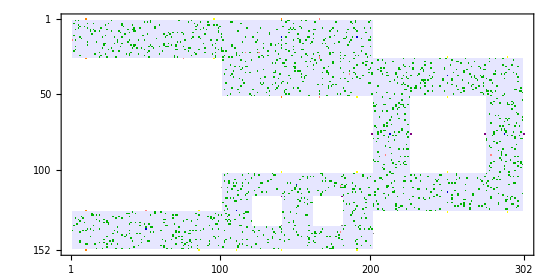

```mathematica
MatrixPlot[Model[[1]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

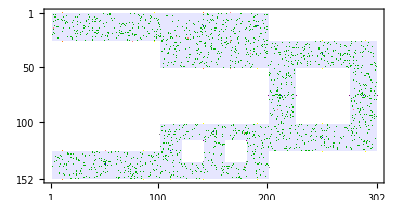

```mathematica
MatrixPlot[Model[[2]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

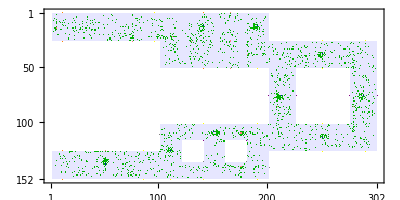

```mathematica
MatrixPlot[Model[[5]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

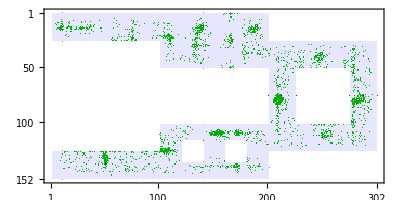

```mathematica
MatrixPlot[Model[[10]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

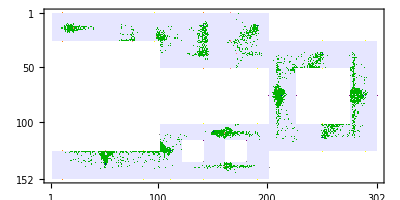

```mathematica
MatrixPlot[Model[[20]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

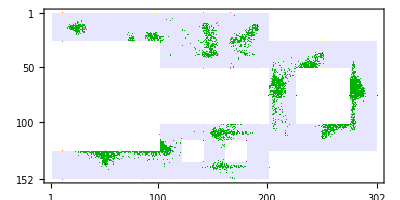

```mathematica
MatrixPlot[Model[[30]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

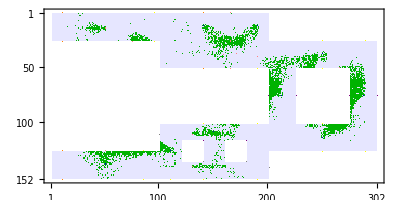

```mathematica
MatrixPlot[Model[[50]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

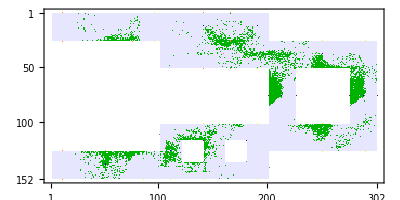

```mathematica
MatrixPlot[Model[[75]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

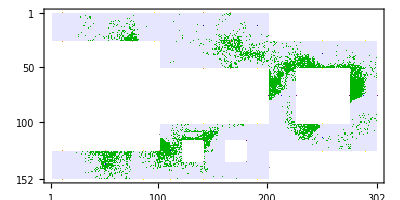

```mathematica
MatrixPlot[Model[[100]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

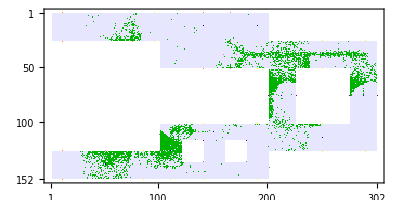

```mathematica
MatrixPlot[Model[[150]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

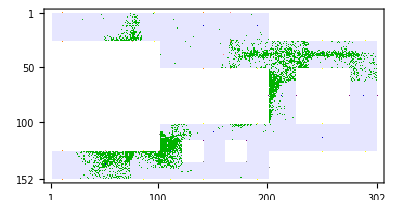

```mathematica
MatrixPlot[Model[[200]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

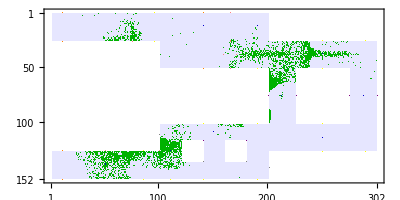

```mathematica
MatrixPlot[Model[[250]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

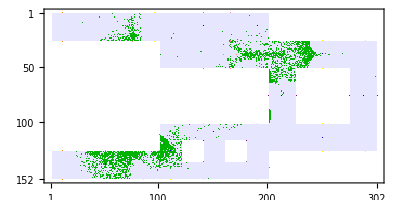

```mathematica
MatrixPlot[Model[[300]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

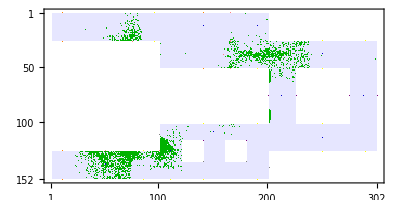

```mathematica
MatrixPlot[Model[[350]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

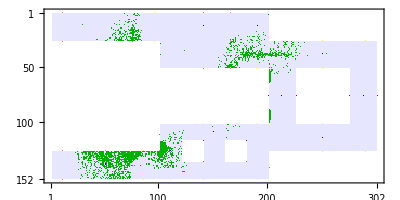

```mathematica
MatrixPlot[Model[[400]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

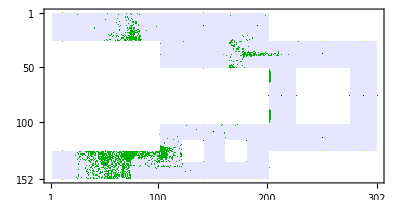

```mathematica
MatrixPlot[Model[[450]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

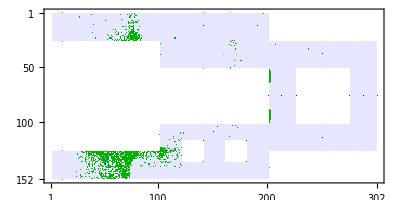

```mathematica
MatrixPlot[Model[[500]],ColorRules->{0->Lighter[Blue,0.9],1->White,2->Darker[Blue,0.2],3->Lighter[Red,0.5],4->Darker[Green,0.3],5->Yellow,6->Orange,7->Purple,8->Gray,9->Black,10->Pink}]
```

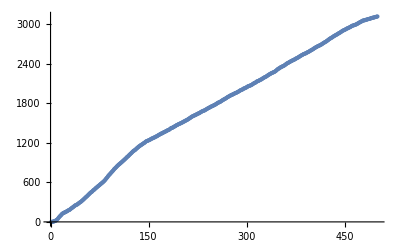

Part::partd: Part specification PPLPath⟦1⟧ is longer than depth of object.

```mathematica
ListPlot[Escape]
```

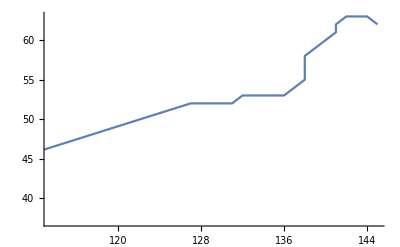

```mathematica
ListPlot[Complement[PPLPath[[28]],{-1,-1}],Joined->True]
```

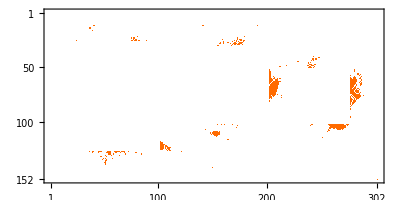

```mathematica
MatrixPlot[CollisionReport[[50]]]
```

```mathematica
PIndex[[102]][[176]]
```

1855

```mathematica
defaultMode[[1855]]
```

0

```mathematica
Aim[[1855]]
```

0

```mathematica
distExt
```

{10000000,10000000,10000000,10000000,10000000,10000000}